```mathematica
Get[NotebookDirectory[]<>"kCurves.wl"]
```

```mathematica
kCurveOpen[{{-1,0},{0,1},{1,0},{2,1}}]
```

{{{-1,0},{-0.08187,1.71183},{0.5,0.5}},{{0.5,0.5},{1.08187,-0.711831},{2,1}}}

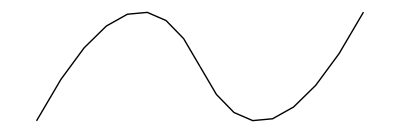

```mathematica
Graphics[BezierCurve[%]]
```

```mathematica
Manipulate[Graphics[BezierCurve[kCurveClosed[pts]],PlotRange->{{-5,5},{-5,5}}],{{pts,{{-1,0},{0,1},{1,0},{2,1}}},Locator}]
```